```mathematica
F[x_]:=PrimePi/@Flatten[ConstantArray@@@FactorInteger[x]]
```

```mathematica
A112798[r_]:=Flatten[Table[F[x],{x,2,r}]]
```

```mathematica
A112798[100]
```

{1,2,1,1,3,1,2,4,1,1,1,2,2,1,3,5,1,1,2,6,1,4,2,3,1,1,1,1,7,1,2,2,8,1,1,3,2,4,1,5,9,1,1,1,2,3,3,1,6,2,2,2,1,1,4,10,1,2,3,11,1,1,1,1,1,2,5,1,7,3,4,1,1,2,2,12,1,8,2,6,1,1,1,3,13,1,2,4,14,1,1,5,2,2,3,1,9,15,1,1,1,1,2,4,4,1,3,3,2,7,1,1,6,16,1,2,2,2,3,5,1,1,1,4,2,8,1,10,17,1,1,2,3,18,1,11,2,2,4,1,1,1,1,1,1,3,6,1,2,5,19,1,1,7,2,9,1,3,4,20,1,1,1,2,2,21,1,12,2,3,3,1,1,8,4,5,1,2,6,22,1,1,1,1,3,2,2,2,2,1,13,23,1,1,2,4,3,7,1,14,2,10,1,1,1,5,24,1,2,2,3,4,6,1,1,9,2,11,1,15,3,8,1,1,1,1,1,2,25,1,4,4,2,2,5,1,1,3,3}

```mathematica
Flatten[Table[PrimePi/@Flatten[ConstantArray@@@FactorInteger[x]],{x,2,100}]]
```

{1,2,1,1,3,1,2,4,1,1,1,2,2,1,3,5,1,1,2,6,1,4,2,3,1,1,1,1,7,1,2,2,8,1,1,3,2,4,1,5,9,1,1,1,2,3,3,1,6,2,2,2,1,1,4,10,1,2,3,11,1,1,1,1,1,2,5,1,7,3,4,1,1,2,2,12,1,8,2,6,1,1,1,3,13,1,2,4,14,1,1,5,2,2,3,1,9,15,1,1,1,1,2,4,4,1,3,3,2,7,1,1,6,16,1,2,2,2,3,5,1,1,1,4,2,8,1,10,17,1,1,2,3,18,1,11,2,2,4,1,1,1,1,1,1,3,6,1,2,5,19,1,1,7,2,9,1,3,4,20,1,1,1,2,2,21,1,12,2,3,3,1,1,8,4,5,1,2,6,22,1,1,1,1,3,2,2,2,2,1,13,23,1,1,2,4,3,7,1,14,2,10,1,1,1,5,24,1,2,2,3,4,6,1,1,9,2,11,1,15,3,8,1,1,1,1,1,2,25,1,4,4,2,2,5,1,1,3,3}

```mathematica
PrimePi/@Flatten[Table[#1,{#2}]&@@@FactorInteger@#]&/@Range@100//Flatten//Rest
```

{1,2,1,1,3,1,2,4,1,1,1,2,2,1,3,5,1,1,2,6,1,4,2,3,1,1,1,1,7,1,2,2,8,1,1,3,2,4,1,5,9,1,1,1,2,3,3,1,6,2,2,2,1,1,4,10,1,2,3,11,1,1,1,1,1,2,5,1,7,3,4,1,1,2,2,12,1,8,2,6,1,1,1,3,13,1,2,4,14,1,1,5,2,2,3,1,9,15,1,1,1,1,2,4,4,1,3,3,2,7,1,1,6,16,1,2,2,2,3,5,1,1,1,4,2,8,1,10,17,1,1,2,3,18,1,11,2,2,4,1,1,1,1,1,1,3,6,1,2,5,19,1,1,7,2,9,1,3,4,20,1,1,1,2,2,21,1,12,2,3,3,1,1,8,4,5,1,2,6,22,1,1,1,1,3,2,2,2,2,1,13,23,1,1,2,4,3,7,1,14,2,10,1,1,1,5,24,1,2,2,3,4,6,1,1,9,2,11,1,15,3,8,1,1,1,1,1,2,25,1,4,4,2,2,5,1,1,3,3}

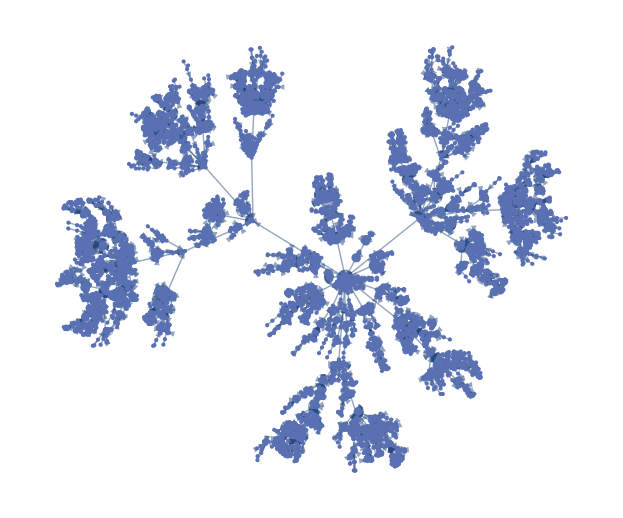

```mathematica
Graph[Table[x->Total[FactorInteger[x-1][[All,1]]],{x,1,10000}]]
```

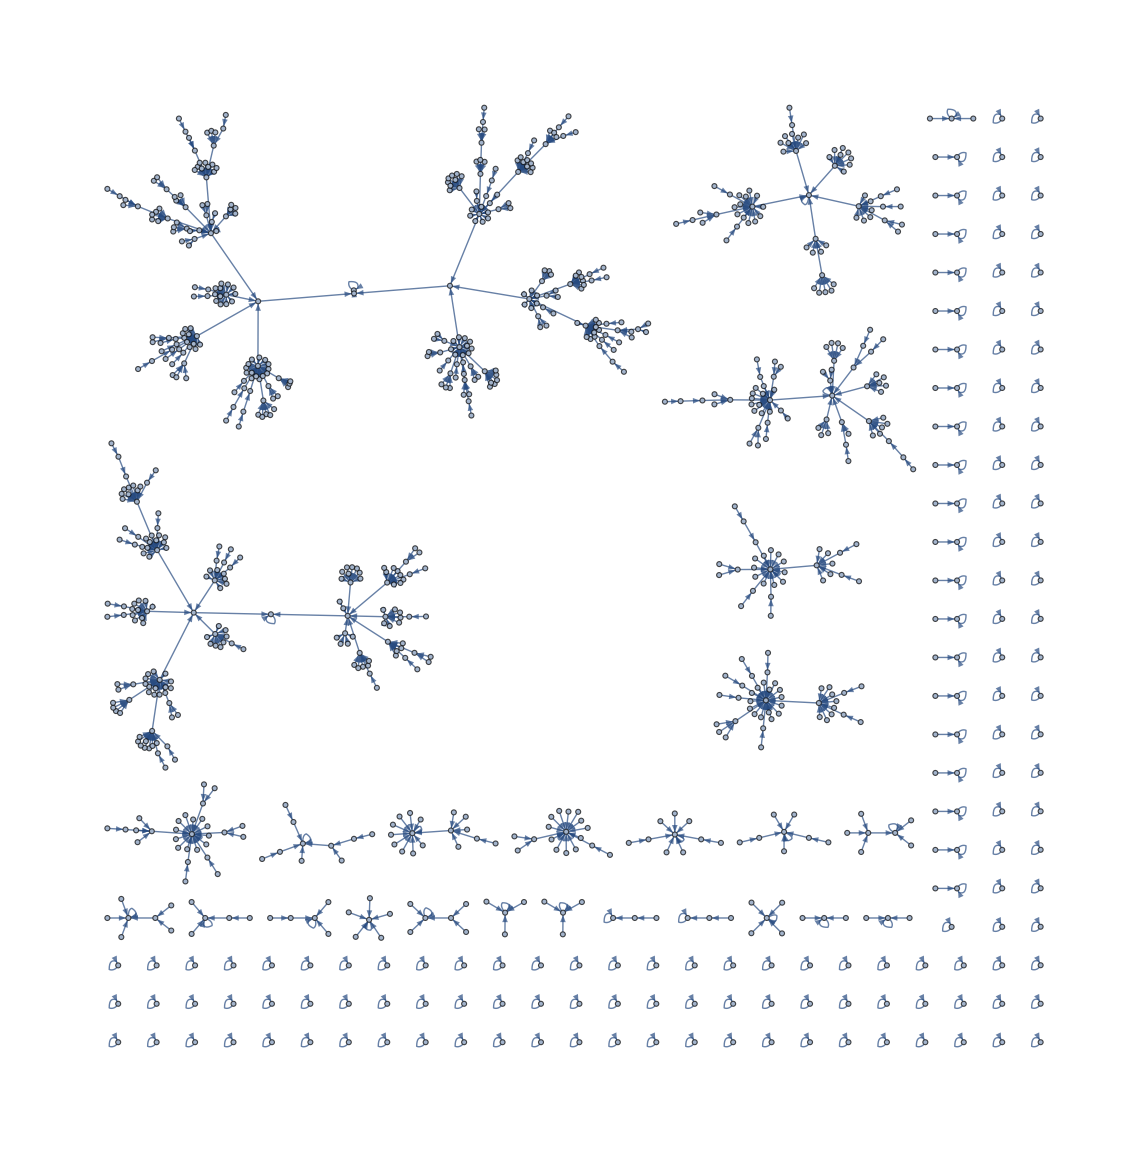

```mathematica
Graph[Table[x->Total[Flatten[ConstantArray@@@FactorInteger[x]]],{x,5,1000}]]
```